```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
(*Constants*)
RESISTANCE=2000;
MAGVOLTAGES=N[Range[0,25,5]];
VRTHRESH=0;
MAGVALUES=Association[{0.-> 0.},{2.5-> 0.061},{5.-> 0.107},{7.5-> 0.157},{10.-> 0.205},{12.5-> 0.251},{15.-> 0.294},{17.5-> 0.335},{20.-> 0.378},{22.5-> 0.417},{25.-> 0.457}];
TESTLIST={{{1,3},{2,4},{5,10}},{{3,9},{6,8},{2,5}}};
MAGFIELDS=mag[#]&/@MAGVOLTAGES;
```

```mathematica
(*Get mag field from mag voltage. The mag field is accurate to two decimal places.*)
mag[v_]:=Module[
{a,b},
If[KeyExistsQ[MAGVALUES,v],
MAGVALUES[v],
a v+b/.{a->0.017629090909090907,b->0.023799999999999957}]
];
```

```mathematica
(*Function that transforms the raw data into lists of {magnetic field, probe voltage, probe current, hall voltage}.
The list of data to be transformed has elements of {mag voltage, total voltage, resistance voltage, hall voltage}.*)
transData[dat_]:=Module[
{transDat},
transDat=dat;
(*Discarding low resistance voltages due to unstable magnetic field in this regime.*)
transDat=Select[transDat,#[[3]]>=VRTHRESH&];
transDat={mag[#[[1]]],#[[2]]-#[[3]],(#[[3]])/RESISTANCE,-#[[4]]}&/@transDat;
transDat
];
```

```mathematica
(*Transform a list of data {dat1, dat2, dat3} in the tranformed format.*)
transAllData[listOfData_]:=transData[#]&/@listOfData;
```

```mathematica
(*This function takes in all the tranformed data at a certain temperature and extracts a list of {B*I, V_hall}.
The original list is in terms of {magnetic field, probe voltage, probe current, hall voltage}*)
getBIList[dat_]:=Module[
{biList},
biList={#[[1]]*#[[3]],#[[4]]}&/@dat;
biList
];
```

```mathematica
(*Plot V_hall vs. B*I plots for each dat that belongs to a certain temperature.
dats: a list of dat where each dat belongs to a certain temperature.*)
plotBILists[dats_,legends_,xCord_,yCord_,axesLabel_:None, fontSize_:16]:=Module[
{biDats},
biDats=getBIList[#]&/@dats;
plotLists[biDats,f,legends,xCord,yCord,axesLabel,fontSize]
];
```

```mathematica
(**This function takes in all the transformed data at a certain temperature and extracts a list of {I, V_probe} for a certain magnetic field voltage. Again, dat is of {magnetic field, probe voltage, probe current, hall voltage}.
dat: the transformed data for a certain temperature.*)
getIVList[dat_,magV_]:=Module[
{ivDat},
(*First, we want to extract all the data with the desired magnetic field.*)
ivDat=Select[dat,#[[1]]==mag[magV]&];
ivDat={#[[3]],#[[2]]}&/@ivDat;
ivDat
];
```

```mathematica
(*Get all the ivDat lists for a certain temperature.*)
getIVListsForTemp[dat_]:=getIVList[dat,#]&/@MAGVOLTAGES;
```

```mathematica
(*dats: a list of sublists where each sublist denotes a certain temperature.*)
plotIVListsForTemps[dats_,legends_,xCor_]:=Module[
{ivDats,ivPlots,fits,x,resistances,rErrs,tPlots},
ivDats=getIVListsForTemp[#]&/@dats;
ivPlots=plotLists[#,f,legends,xCor,"V_p",{"I (A)","V_p (volts)"}]&/@ivDats;

fits=#[[3]]&/@ivPlots;
(*Now fits has three sublists of rules where each sublist corresponds to a temperature.*)
resistances=Map[Function[x,Coefficient[#,xCor]&/@x],fits];
resistances=Map[Function[x,MapThread[{#2,#1}&,{x,MAGFIELDS}]],resistances];
rErrs=Map[Function[tPlots,#[[3]]&/@tPlots[[4]]],ivPlots];
{ivPlots,resistances,rErrs}
];
(*Obtain the Hall probe resistance values and their corresponding standard errors for different temperatures and for different magnetic fields.
dats: the transformed list of sublists of the experimental data.*)
getRwithErrs[dats_]:=Module[
{results,i,rDats,rErrs},
results=plotIVListsForTemps[dats,Range[0,25,5],i];
rDats=results[[2]];
rErrs=results[[3]];
{rDats,rErrs}
];
```

```mathematica
(*Plot the resistances vs. magnetic fields and their errors for the Hall probe at different temperatures.*)
plotRwithErrs[dats_]:=Module[
{rDats,rErrs,plots},
{rDats,rErrs}=getRwithErrs[dats];
plots=plotErrLists[rDats,rErrs,"B (T)","R_p (Ohm)",{"T ≈ 22 °C","T ≈ 69 °C", "T ≈ 101 °C"},False];
plots
];
```

```mathematica
(*Plot (R-Subscript[R, 0]) vs. B^2 for different temperatures with errors.*)
plotRB2withErrs[dats_]:=Module[
{rDats,rErrs,plots,rDat,rErr,rLen},
{rDats,rErrs}=getRwithErrs[dats];
rLen=Length[rErrs[[1]]];

rDats=Map[Function[rDat,{(#[[1]])^2,#[[2]]-rDat[[1]][[2]]}&/@rDat],rDats];
rErrs=Map[Function[rErr,MapThread[If[#2==1,{0,0},{-#1-rErr[[1]],#1+rErr[[1]]}]&,{rErr,Range[rLen]}]],rErrs];

plots=MapThread[plotErrLists[{#1},{#2},"B^2 (T^2)","R_p(B)-R_p(B=0) (Ohm)",#3,True]&,{rDats,rErrs,{"T ≈ 22 °C","T ≈ 69 °C", "T ≈ 101 °C"}}];

{plots,rDats,rErrs}
];
```

```mathematica
f[a_,b_,x_]:=a x+b;
```

```mathematica
(*A general-purpose function that, given a list of lists of {x,y}, plots the second-order lists on the same graph
with a straight fitting line assigned to each second-order list.
dats: a list of dat, where a dat is a list of {x,y}.
f: a function that, when taking 3 variables a, b and x, gives ax+b.
legends: legends is a list of labels for each dat.
xCord: the variable that we want to use as the fitting function. This will be useful in visualizing
the fitting function by Tooltip.*)
plotLists[dats_,f_,legends_,xCord_, yCord_,axesLabel_:None, fontSize_:16]:=Module[
{fits,plots,xRanges,xRange,x,a,b,totPlot,indiPlots,lms,lmfits},
(*First, we want to find the fitting lines for each sub-list.*)
lms=LinearModelFit[#,xCord,xCord]&/@dats;
fits=FindFit[#,f[a,b,x],{a,b},x]&/@dats;

fits=(f[a,b,xCord]/.#)&/@fits;
lmfits={Normal[#],#["ParameterTable"],#["ParameterErrors"][[2]]}&/@lms;

(*Want to find the x ranges for the individual fits. This means that for each sublist, we want to find its x_min and x_max.
dats is a list of sub-lists. Each sub-list contains {x,y}.*)
xRanges={Min[Map[Function[x,x[[1]]],#]],Max[Map[Function[x,x[[1]]],#]]}&/@dats;

(*Then we want to find the common x_min and x_max for all the {x_min, x_max} in xRanges so that we can
plot all the fitting lines with a common range.*)
xRange={Min[#[[1]]&/@xRanges], Max[#[[2]]&/@xRanges]};

totPlot=Show[ListPlot[Tooltip[dats]],Plot[Tooltip[Evaluate[fits]],{xCord,xRange[[1]],xRange[[2]]},PlotLegends->Placed[legends,{1,0.5}]],AxesLabel-> axesLabel, BaseStyle-> {FontSize-> fontSize}];

(*In addition to putting all the individual dat plots in the same graph, we also want to ouput each individual graph by itself.*)

indiPlots=MapThread[Show[ListPlot[Tooltip[#1]],Plot[Tooltip[Evaluate[#2]],{xCord,#3[[1]],#3[[2]]},PlotLegends->Placed[#4,{1,0.5}]],PlotLabel->yCord<>" = "<>ToString[Evaluate[#2]],AxesLabel-> axesLabel,BaseStyle-> {FontSize-> fontSize}]&,{dats,fits,xRanges,legends}];
{totPlot,indiPlots,fits,lmfits}
];
```

```mathematica
(*Gives an error bar list plot for dats.*)
plotErrLists[dats_, errs_,xCord_,yCord_,legends_:None,twoBounds_:False]:=Module[
{dat,err,errDats,errPlot},
errDats=If[!twoBounds,
MapThread[Function[{dat, err},MapThread[{#1,ErrorBar[#2]}&,{dat,err}]],{dats,errs}],
MapThread[Function[{dat, err},MapThread[{#1,ErrorBar[{#2[[1]],#2[[2]]}]}&,{dat,err}]],{dats,errs}]
];
errPlot=Show[ErrorListPlot[Tooltip[errDats],PlotLegends-> Placed[legends,{1,0.5}],Joined-> True,PlotMarkers-> {●,12},BaseStyle->{FontSize-> 16},AxesLabel->{xCord,yCord},PlotRange->All],PlotRange-> All];
errPlot
];
```

```mathematica
d22=Import["/Users/benxgh1996/Desktop/Hall/results.xlsx",{"Data",2,Range[2,67],Range[1,4]}];
```

```mathematica
d69=Import["/Users/benxgh1996/Desktop/Hall/results.xlsx",{"Data",3,Range[2,67],Range[1,4]}];
```

```mathematica
d101=Import["/Users/benxgh1996/Desktop/Hall/results.xlsx",{"Data",4,Range[2,67],Range[1,4]}];
```

```mathematica
{d22, d69, d101}=transAllData[{d22, d69, d101}];
```

```mathematica
allData={d22, d69, d101};
```

```mathematica
biResults=plotBILists[allData,{"T ≈ 22 °C","T ≈ 69 °C", "T ≈ 101 °C"},BI,"V_h",{"BI (TA)","V_h (volts)"},16];
```

```mathematica
plotIVListsForTemps[allData,Range[0,25,5],i];
```

```mathematica
getRwithErrs[allData]
```

{{{{0.,746.162},{0.107,745.878},{0.205,749.505},{0.294,750.624},{0.378,749.422},{0.457,766.057}},{{0.,832.285},{0.107,830.206},{0.205,826.245},{0.294,830.979},{0.378,837.572},{0.457,832.96}},{{0.,900.893},{0.107,889.987},{0.205,893.909},{0.294,898.792},{0.378,904.123},{0.457,906.474}}},{{0.384282,1.88269,3.22693,4.08354,3.5677,2.60271},{0.971428,2.26877,2.47446,3.12524,4.19521,3.39193},{1.03492,1.82993,2.59947,4.7684,3.89776,2.44946}}}

```mathematica
rdats=Map[Function[rdat,#[[2]]&/@rdat],getRwithErrs[allData][[1]]]
```

{{746.162,745.878,749.505,750.624,749.422,766.057},{832.285,830.206,826.245,830.979,837.572,832.96},{900.893,889.987,893.909,898.792,904.123,906.474}}

```mathematica
StandardDeviation@#&/@rdats
```

{7.49362,3.71239,6.21112}

```mathematica
Mean@#&/@rdats
```

{751.275,831.708,899.03}

```mathematica
LinearModelFit[{{22,750},{69,830},{101,900}},{x},{x}]
```

FittedModel[706.084+1.8841 x]

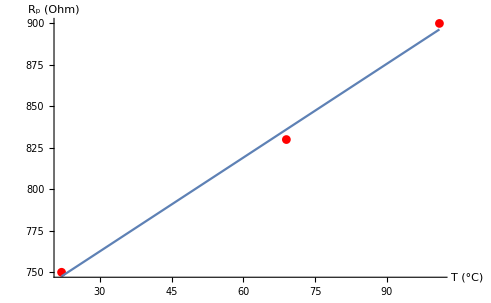

```mathematica
Show[ListPlot[{{22,750},{69,830},{101,900}},PlotStyle->Red],Plot[FittedModel[Panel[Short[706.0840194215748+1.88410386320456 x,2],FrameMargins->5]][x],{x,22,101}],AxesLabel-> {"T (°C)","R_p (Ohm)"},BaseStyle-> {FontSize-> 16}]
```

```mathematica
FittedModel[706.0840194215748+1.88410386320456 x]["RSquared"]
```

0.995008

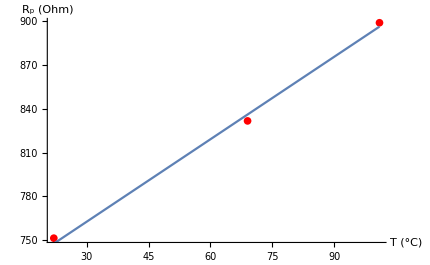

```mathematica
Show[ListPlot[{{22,751.2747381775749},{69,831.7078018508925},{101,899.029727855028}},PlotStyle->Red],Plot[FittedModel[Panel[Short[706.0840194215748+1.88410386320456 x,2],FrameMargins->5]][x],{x,22,101}],AxesLabel-> {"T (°C)","R_p (Ohm)"},BaseStyle-> {FontSize-> 16}]
```

```mathematica
plotRwithErrs[allData]
```

-Graphics-

```mathematica
plotRB2withErrs[allData]
```

{{-Graphics-,-Graphics-,-Graphics-},{{{0.,0.},{0.011449,-0.283413},{0.042025,3.34377},{0.086436,4.46226},{0.142884,3.26074},{0.208849,19.8955}},{{0.,0.},{0.011449,-2.07892},{0.042025,-6.03976},{0.086436,-1.30655},{0.142884,5.28642},{0.208849,0.674658}},{{0.,0.},{0.011449,-10.9061},{0.042025,-6.98381},{0.086436,-2.10047},{0.142884,3.2306},{0.208849,5.58138}}},{{{0,0},{-2.26697,2.26697},{-3.61121,3.61121},{-4.46783,4.46783},{-3.95198,3.95198},{-2.98699,2.98699}},{{0,0},{-3.2402,3.2402},{-3.44589,3.44589},{-4.09667,4.09667},{-5.16664,5.16664},{-4.36336,4.36336}},{{0,0},{-2.86485,2.86485},{-3.63439,3.63439},{-5.80333,5.80333},{-4.93268,4.93268},{-3.48438,3.48438}}}}

```mathematica
b2Plots=plotRB2withErrs[allData][[1]]
```

{-Graphics-,-Graphics-,-Graphics-}

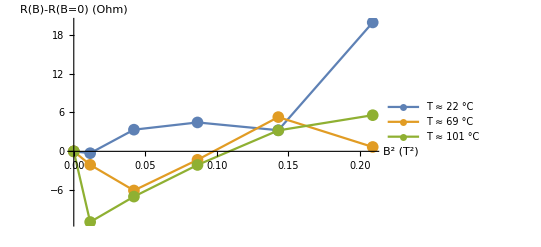

```mathematica
Show[ListPlot[Tooltip[br],PlotLegends-> {"T ≈ 22 °C","T ≈ 69 °C", "T ≈ 101 °C"},AxesLabel-> {"B^2 (T^2)","R(B)-R(B=0) (Ohm)"},Joined-> True,BaseStyle-> {FontSize-> 16},PlotMarkers-> {●,12}],PlotRange-> All]
```

```mathematica
Graphics[Show[ErrorListPlot[{{{{1,2},ErrorBar[3]},{{3,4},ErrorBar[5]}},{{{2,6},ErrorBar[3]},{{4,3},ErrorBar[5]}}},Joined-> True,PlotMarkers-> {●,12}],PlotRange-> All]];
```

```mathematica
plotErrLists[{{{1,2},{3,4},{5,7}},{{2,6},{3,9},{6,1}}}, {{{-2,3},{-1,2},{0,1}},{{-5,4},{-3,2},{-6,5}}},x,y,{1,2},False];
```

```mathematica
plotErrLists[{{{1,2},{3,4},{5,7}}}, {{{-2,3},{-1,2},{0,1}}},x,y,{1,2},False];
```